## Problem 6

### Problem Statement

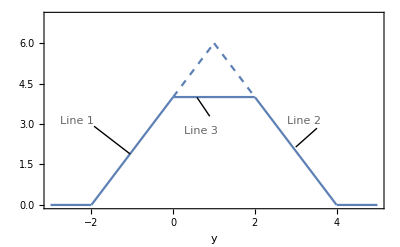

Write an equation for the solid blue lines in the above graph in terms of the difference of two tri functions

### Compact Solution

Define and graph the tri function

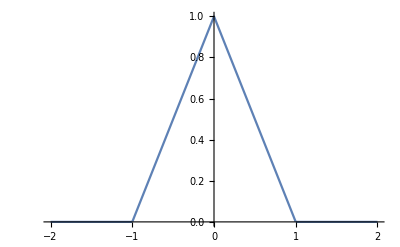

```mathematica
tri[x_]:= Piecewise[{{1 - Abs[x], Abs[x]≤1}, {0, True}}];
Plot[tri[x],{x,-2,2}]
```

A function which describes the graph given in the problem is f[x] = 6tri[(x-1)/3] -2tri[(x-1)]

### Detailed Solution

The functions 2tri[x/2] and 6 tri[x/6] also have  slopes of 2.

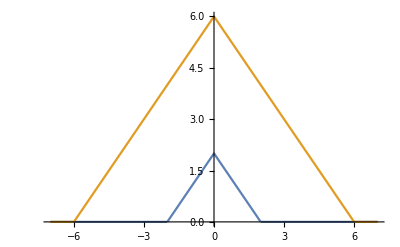

```mathematica
Plot[{2tri[x/2],6tri[x/6]},{x,-7,7}]
```

The above graph suggests that taking the difference of these two functions may give us what we want.

6tri[x/6] -2tri[x/2]has the correct shape for the desired function and also has the correct amplitude.  However the base and peak are twice as wise as the target function.

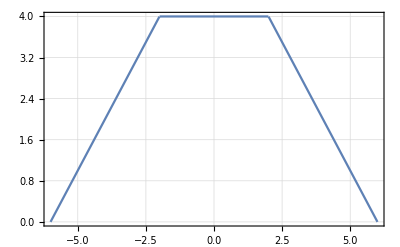

```mathematica
Plot[6tri[x/6] -2tri[x/2], {x,-6,6}, Frame-> True, GridLines-> Automatic]
```

Decrease the width of the function by replacing x by 2x.  Now the width of the function at the base and at the peak are respectively 6 and 2 respectively and match the properties of the target function.

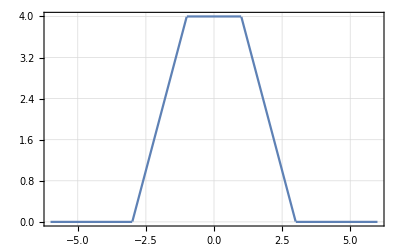

```mathematica
Plot[6tri[(2x)/6] -2tri[(2x)/2], {x,-6,6}, Frame-> True, GridLines-> Automatic]
```

Shift the above function one unit to the right and it should match the target function.

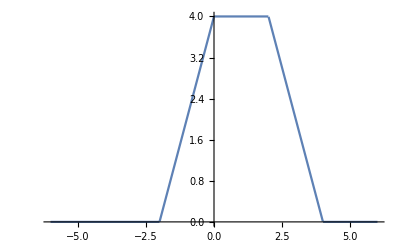

```mathematica
Plot[6tri[(x-1)/3] -2tri[(x-1)], {x,-6,6}]
```

A function which describes the graph given in the problem is f[x] = 6tri[(x-1)/3] -2tri[(x-1)]